```mathematica
Remove["Global`*"]
```

```mathematica
g:=9.8
```

```mathematica
h:=10
```

```mathematica
θ:=Pi/12
```

```mathematica
Subscript[v, 0]:=5
```

```mathematica
x[t_]:=Subscript[v, 0]*Cos[θ]*t
```

```mathematica
y[t_]:=h+Subscript[v, 0]*Sin[θ]*t-0.5*g*t^2
```

```mathematica
time=Solve[{y[t]==0},t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.102041 (-0.316228 √(125.+196. h-125. Cos[2. θ])+5. Sin[θ])},{t→0.102041 (0.316228 √(125.+196. h-125. Cos[2. θ])+5. Sin[θ])}}

```mathematica
Note: Solving for y=0.
```

```mathematica
x[t/.time[[2,1]]]
```

0.510204 Cos[θ] (0.316228 √(125.+196. h-125. Cos[2. θ])+5. Sin[θ])

```mathematica
Note: Getting range(i.e  x[t] for the positive value)
```

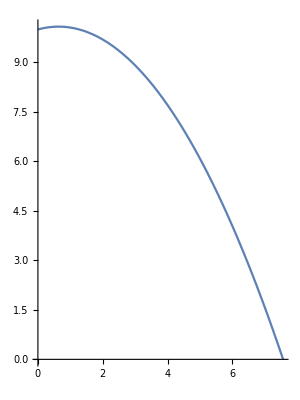

```mathematica
ParametricPlot[{x[t],y[t]}/.{θ->π/12,h->10},{t,0,t/.time[[2,1]]/.{θ->π/12,h->10}}]
```

```mathematica
Note:Parametric plot for h=5m and θ=(15^0).
```

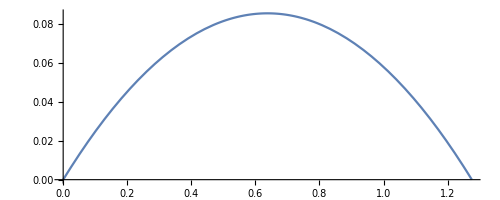
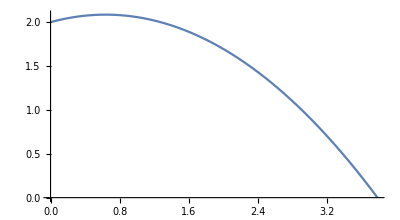
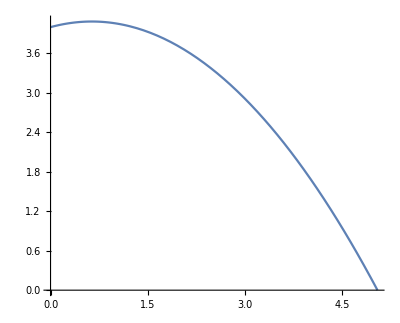
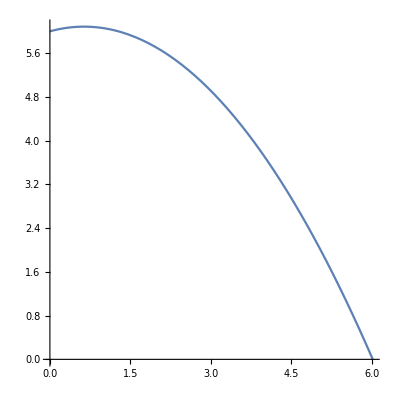
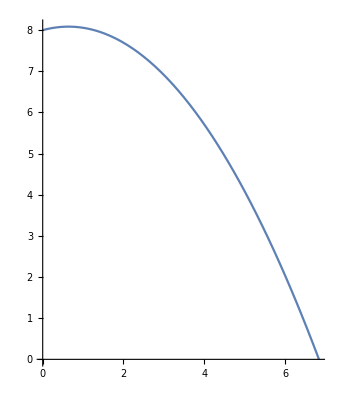
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Evaluate@Table[ParametricPlot[{x[t],y[t]}/.{θ->Pi/12},{t,0, t/.time[[2,1]]/.{θ->Pi/12}}],{h,0,10,2}]
```

```mathematica
Note:parametric plots for varying h.
```

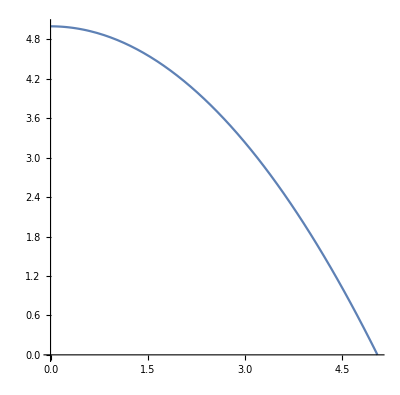
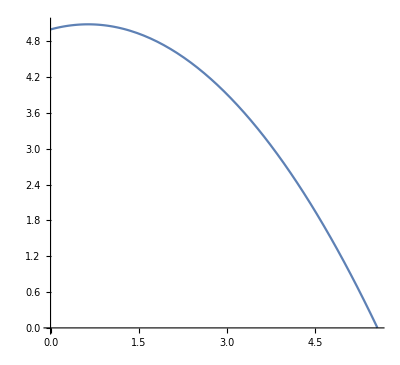
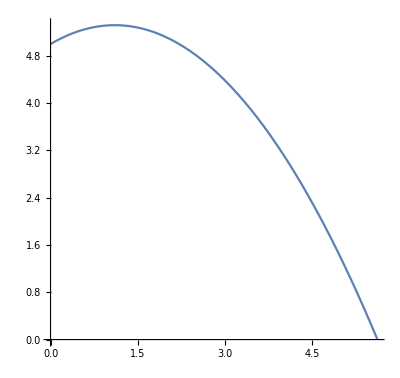
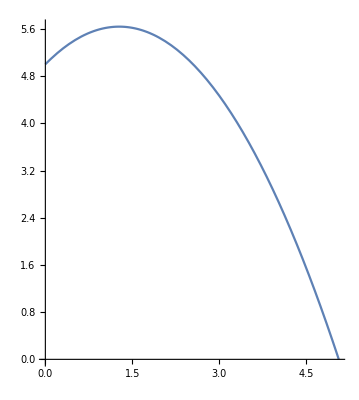
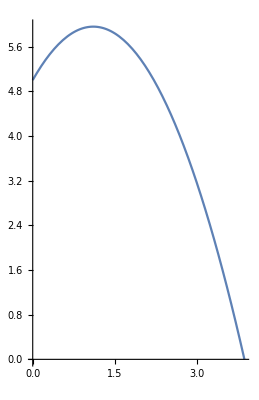
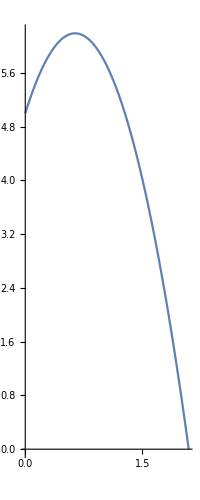
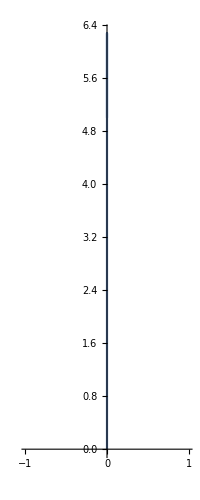

```mathematica
Evaluate@Table[ParametricPlot[{x[t],y[t]}/.{h->5},{t,0,t/.time[[2,1]]/.{h->5}}],{θ,0,Pi/2,Pi/12}]
```

```mathematica
Note: parametric plots for varying θ.
```

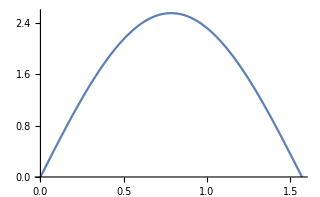
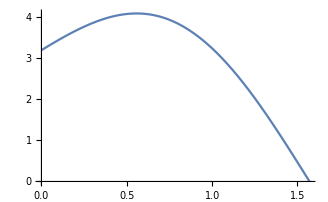
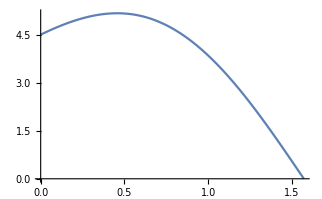
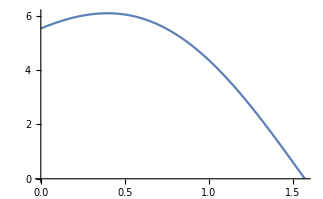
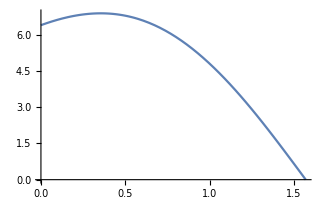
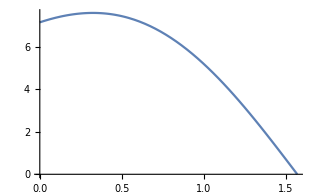

```mathematica
Evaluate@Table[Plot[x[t/.time[[2,1]]], {θ,0,Pi/2}],{h,0,10,2}]
```

```mathematica
note: range vs θ for various h values.
```

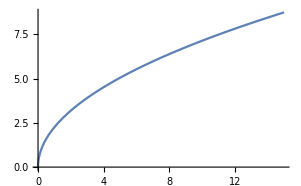
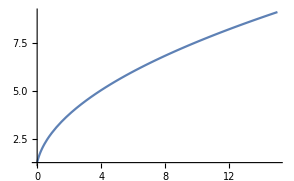
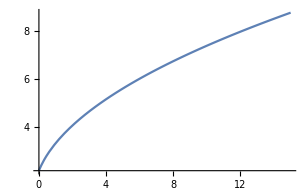
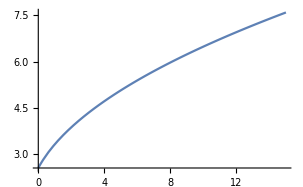
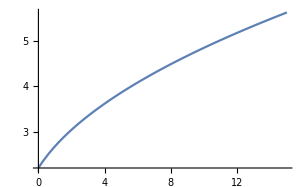
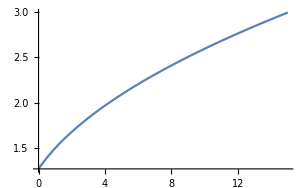
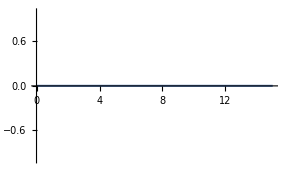

```mathematica
Evaluate@Table[Plot[x[t/.time[[2,1]]], {h,0,15}],{θ,0,Pi/2,Pi/12}]
```

```mathematica
Note: range vs h for various values of θ.
```

```mathematica
4*N[Sum[(-1)^n/(2*n+1),{n,0,9}]]
```

3.04184

```mathematica
NumberForm[3.0418396189294024,16]
```

3.041839618929402

```mathematica
Accuracy only in the units place.
```

```mathematica
4*N[Sum[(-1)^n/(2*n+1),{n,0,49}]]
```

3.12159

```mathematica
NumberForm[3.1215946525910105,16]
```

3.12159465259101

```mathematica
Accuracy till the first decimal place.
```

```mathematica
4*N[Sum[(-1)^n/(2*n+1),{n,0,9}]+(-1)^(n+1)/(4*(n+1))/.{n->9}]
```

3.14184

```mathematica
Accuracy till third decimal place.
```

```mathematica
4*N[Sum[(-1)^n/(2*n+1),{n,0,9}]+(n+1)/((2n+2)^2+1)/.{n->9}]
```

3.14159

```mathematica
NumberForm[3.141590242370799,16]
```

3.141590242370799

```mathematica
Accuracy till fifth decimal place.
```

```mathematica
4*N[Sum[(-1)^n/(2*n+1),{n,0,9}]+((n+1)^2+1)/((n+1)*((2*n+2)^2+5))/.{n->9}]
```

3.14159

```mathematica
NumberForm[3.1415927053491552,16]
```

3.141592705349155

```mathematica
Accuracy till the sixth decimal place.
```